```mathematica
Needs["QCDLib`"];
Needs["ErrorBarPlots`"];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

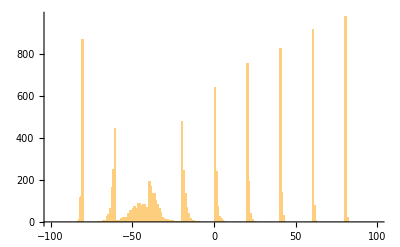

```mathematica
Module[{binActions},
binActions = arrayReshape[readRel[
"sk_test.actions.dat", "Real64"], {10, 1000}];
Print@Table[Rasterize@ListPlot[binActions⟦i⟧, Joined->True], {i, 10}];
Print@Histogram[Flatten[binActions], {Range[-100, 100, 1]}];
];
```

```mathematica
approxTrueSamples[β_, V_, N_] := Module[{samples},
samples = Total[-β Cos[RandomVariate[VonMisesDistribution[0,β], {N, V}]], {2}];
samples];
```

```mathematica
samples = approxTrueSamples[1.0, 100, 100000];
```

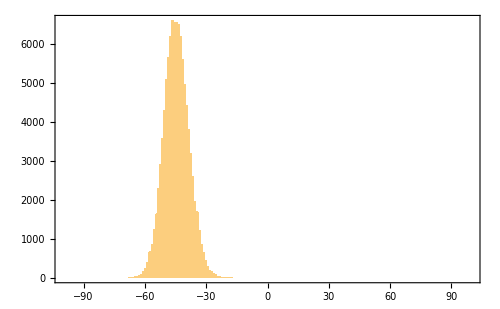

```mathematica
Histogram[samples, {Range[-100, 100, 1]}, frameOpts[]]
```

```mathematica
skdDist = SmoothKernelDistribution[samples, Automatic, {"Bounded", {-100, 100}, "Gaussian"}];
```

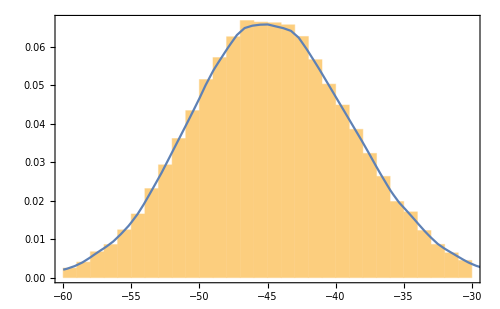

```mathematica
Show[
Histogram[samples, {Range[-60, -30, 1]}, "PDF", frameOpts[]],
Plot[PDF[skdDist, x], {x, -60, 30}]
]
```

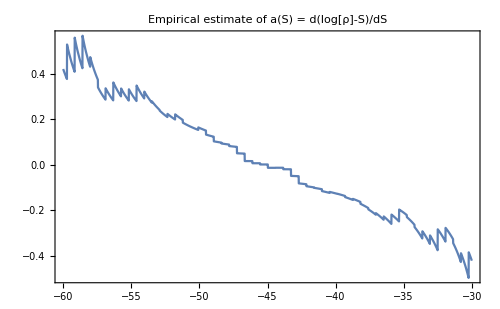

```mathematica
Plot[
Evaluate[D[Log[PDF[skdDist, x]], x]], {x, -60, -30},
Evaluate[frameOpts[]],
PlotLabel->title["Empirical estimate of a(S) = d(log[ρ]-S)/dS"]]
```

```mathematica
D[Log[PDF[skdDist, x]], x] /. {x ->  -39.5}
```

-0.133319

```mathematica
oneVMsamples = Cos[RandomVariate[VonMisesDistribution[0, 1.0], 1000]];
```

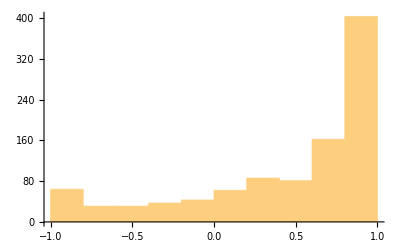

```mathematica
Histogram[oneVMsamples]
```

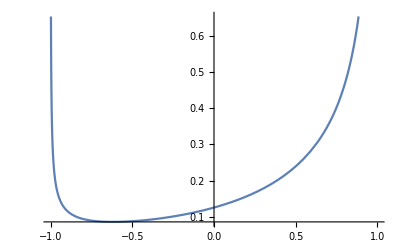

```mathematica
Plot[Exp[1.0 x] / (Sqrt[1-x^2] 2 Pi BesselI[0, 1.0]), {x, -1, 1}]
```

```mathematica
Z[β_] := Integrate[2 Exp[β x] / (2 Pi BesselI[0, β] Sqrt[1 - x^2]), {x, -1, 1}];
```

```mathematica
Z[β]
```

1

```mathematica
Integrate[Exp[β Cos[x]] / (2 Pi BesselI[0, β]), {x, 0, 2Pi}]
```

1

```mathematica
μ[β_] := BesselI[1, β] / BesselI[0, β];
```

```mathematica
{μ[1.0], Mean@oneVMsamples}
```

{0.44639,0.451818}

```mathematica
D[D[BesselI[0, β], β], β]
```

1/2 (BesselI[0,β]+BesselI[2,β])

```mathematica
μ2[β_] := 1/2 (BesselI[0,β]+BesselI[2,β]) / BesselI[0,β];
```

```mathematica
var[β_] := μ2[β] - μ[β]^2;
```

```mathematica
Simplify[var[β]]
```

(BesselI[0,β]^2-2 BesselI[1,β]^2+BesselI[0,β] BesselI[2,β])/(2 BesselI[0,β]^2)

```mathematica
var[1.0]
```

0.354346

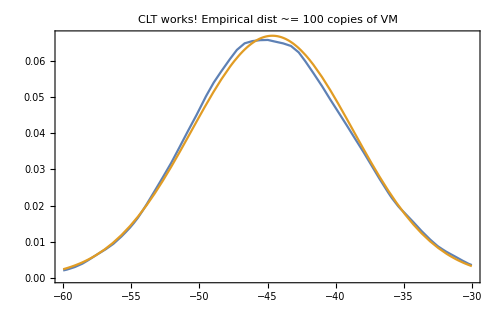

```mathematica
Plot[{
PDF[skdDist, x],
PDF[NormalDistribution[-μ[1.0]*100, Sqrt[var[1.0] 100]], x]
}, {x, -60, -30}, Evaluate[frameOpts[]],
PlotLabel->title["CLT works! Empirical dist ~= 100 copies of VM"]]
```

```mathematica
analyticA[β_, V_, S_] := -(S + V μ[β])/(V var[β]);
```

```mathematica
analyticA[1.0, 100, -39.5]
```

-0.145028